### A fact function

```mathematica
fact[n_Integer]:=If[n==0,1,n fact[n-1]]
```

```mathematica
Array[fact,5]
```

{1,2,6,24,120}

```mathematica
fact[2]//Trace
```

{fact[2],If[2==0,1,2 fact[2-1]],{2==0,False},If[False,1,2 fact[2-1]],2 fact[2-1],{{2-1,1},fact[1],If[1==0,1,1 fact[1-1]],{1==0,False},If[False,1,1 fact[1-1]],1 fact[1-1],{{1-1,0},fact[0],If[0==0,1,0 fact[0-1]],{0==0,True},If[True,1,0 fact[0-1]],1},1 1,1},2 1,2}

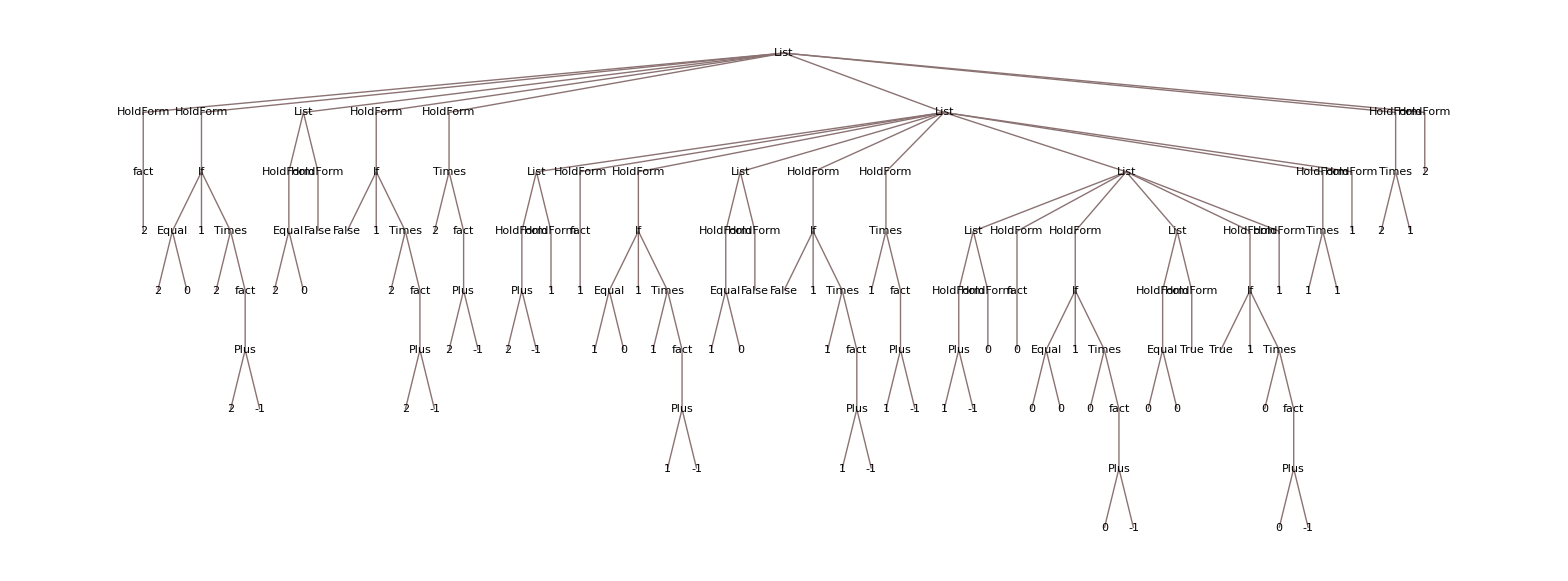

```mathematica
TreeForm[%145]
```